```mathematica
yyyHank[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(18),{d,7,11,0.5}];
DaForceX[x_,y_,t_,k_,w_] = -D[yyyHank[x,y,t,k,w],x];
DaForceY[x_,y_,t_,k_,w_] = -D[yyyHank[x,y,t,k,w],y];
CosDisSqWidth = ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]
```

ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]

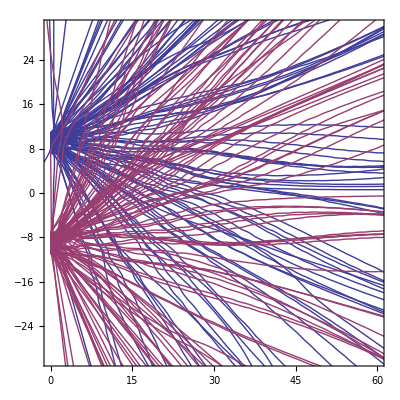

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 250;
xmax = 60;
NMAX=100;
swidth = 2;
phase =0;
MEMORY = 1000;

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMORY)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
];

ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 120;
swidth = 2;
CHUNK = 7*16;
REPEAT = 1000;
CUTTOFF = 40;
phase = 0;
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
MEMORYLIST = {40};

Do[
Close["HydroDoubleSlitAutoP0M"<> ToString[MEMVALUE]<>".dat"]
,{MEMVALUE,MEMORYLIST}]

Do[
Do[
outstream=OpenAppend["HydroDoubleSlitAutoP0M"<> ToString[MEMVALUE]<>".dat"];

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMVALUE)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMVALUE)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMVALUE)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMVALUE)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]

(*Beep[]*)
EmitSound[Play[Sin[1000 t^2],{t,0,1}]];

,{MEMVALUE,MEMORYLIST}];
(*Close[outstream]*)
,{REPEAT}];
```

General::openx: "HydroDoubleSlitAutoP0M40.dat" is not open.

$Aborted

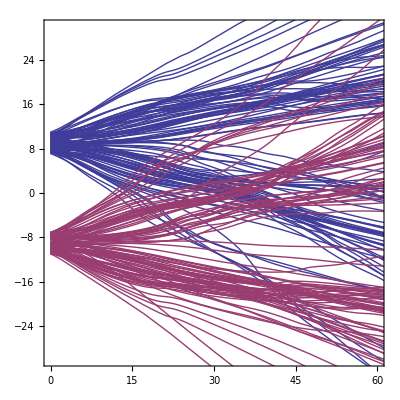

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 0.5;
kkk= 1.0;
disss = 0.005;
tmax = 250;
xmax = 60;
NMAX=100;
swidth = 2;
phase =-1/2;
MEMORY = 1000;

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMORY)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==v000 Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
];

ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 120;
swidth = 2;
CHUNK = 7*16;
REPEAT = 1000;
CUTTOFF = 20;
phase = -1/2;
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
MEMORYLIST = {40};

Do[
Close["HydroDoubleSlitAutoC20M"<> ToString[MEMVALUE]<>".dat"]
,{MEMVALUE,MEMORYLIST}]

Do[
Do[
outstream=OpenAppend["HydroDoubleSlitAutoC20M"<> ToString[MEMVALUE]<>".dat"];

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMVALUE)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMVALUE)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMVALUE)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMVALUE)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]

(*Beep[]*)
EmitSound[Play[Sin[1000 t^2],{t,0,1}]];

,{MEMVALUE,MEMORYLIST}];
(*Close[outstream]*)
,{REPEAT}];
```

$Aborted